# Zero-frequency QNMs

Evaluate the notebook from top to bottom. Place Background_N60_phiM_0.8.m and Background_N60_phiM_1.m in the same directory as this notebook. The spectrum is computed at omega = 0, with eigenvalue (q/(2πT))^2.

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["Results"], CreateDirectory["Results"]];
```

## Code

### Grid generation

Generate the radial Chebyshev grid and its first and second derivative matrices.

```mathematica
Cheb[xmin_,xmax_,Nu_,prec_]:=Block[{M,x,c,X,ΔX,D,D2},
			M=Nu-1;
			x = -Cos[π Range[0,M]/M];
			c = (-1)^Range[0,M] Join[{2},Table[1,{ii,1,M-1}],{2}];
			X = Table[x,{ii,1,Nu}]ᵀ;        
			ΔX = X-Xᵀ;
			D=({c}ᵀ.{c}^-1)/(ΔX+IdentityMatrix@Nu);
			D = D-DiagonalMatrix@Total[Dᵀ];
			x = 1/2 (xmax+xmin+(xmax-xmin) x); 
			D = (2 D)/(xmax-xmin);
			SetPrecision[{x, D, D.D},prec]];
```

### Bulk coefficients

Coefficients of the zero-frequency perturbation equations.

```mathematica
𝒜[u_,D_,D2_,f_,g_,ψ_,V_,T_]:={{{0, 0}, {0, 0}}, 
 {{6*f^2*g^3*Pi^2*T^2*u^3*(2*g - u*D . g)*
    (f*(-12*g*u*D . g + 3*u^2*(D . g)^2 + 
       4*g^2*(3 + u^2*ψ^2 + 2*u^3*ψ*
          D . ψ + u^4*(D . ψ)^2)) - 
     8*g^2*V[u*ψ]), 0}, 
  {0, 9*f*g^2*Pi^2*T^2*u^2*(-2*g + u*D . g)^
     2*(f*(-12*g*u*D . g + 
       3*u^2*(D . g)^2 + 4*g^2*
        (3 + u^2*ψ^2 + 2*u^3*ψ*D . ψ + 
         u^4*(D . ψ)^2)) - 
     8*g^2*V[u*ψ])}}, {{0, 0}, {0, 0}}};
```

```mathematica
ℬ[u_,D_,D2_,f_,g_,ψ_,V_,T_]:={{{0, -3*f*g^3*u*(-2*g + u*D . g)*
    (g*(8*u*(ψ + u*D . ψ)*V[u*ψ] - 
       6*Derivative[1][V][u*ψ]) + 
     3*u*D . g*Derivative[1][V][u*ψ])}, 
  {0, 0}}, {{-2*f*g^3*Pi^2*T^2*u^2*
    (f^2*(27*u^3*(D . g)^3 - 12*g^2*u*D . g*
        (-27 + u^2*ψ^2 + 2*u^3*ψ*D . ψ + 
         u^4*(D . ψ)^2) + 6*g*u^2*
        (D . g)^2*(-27 + 2*u^2*ψ^2 + 
         4*u^3*ψ*D . ψ + 2*u^4*
          (D . ψ)^2) + 8*g^3*
        (-27 + 2*u^4*ψ^4 + 8*u^5*ψ^3*
          D . ψ - 3*u^4*(D . ψ)^2 + 
         2*u^8*(D . ψ)^4 + 3*u^2*ψ^2*
          (-1 + 4*u^4*(D . ψ)^2) + 
         ψ*(-6*u^3*D . ψ + 8*u^7*
            (D . ψ)^3))) - 
     8*f*g*(-3*g*u*D . g + 
       3*u^2*(D . g)^2 + 2*g^2*
        (-3 + 4*u^2*ψ^2 + 8*u^3*ψ*
          D . ψ + 4*u^4*(D . ψ)^2))*
      V[u*ψ] + 64*g^3*V[u*ψ]^2), 0}, 
  {0, 3*g*Pi^2*T^2*u*(2*g - u*D . g)*
    (f^2*(171*g*u^3*(D . g)^3 - 
       18*u^4*(D . g)^4 - 6*g^2*u^2*
        (D . g)^2*(99 + 2*u^2*ψ^2 + 
         4*u^3*ψ*D . ψ + 2*u^4*
          (D . ψ)^2) + 12*g^3*u*D . g*
        (75 + 7*u^2*ψ^2 + 14*u^3*ψ*
          D . ψ + 7*u^4*(D . ψ)^2) + 
       8*g^4*(-63 + 2*u^4*ψ^4 + 
         8*u^5*ψ^3*D . ψ - 15*u^4*
          (D . ψ)^2 + 2*u^8*(D . ψ)^4 + 
         3*u^2*ψ^2*(-5 + 4*u^4*(D . ψ)^
             2) + ψ*(-30*u^3*D . ψ + 
           8*u^7*(D . ψ)^3))) - 
     72*f*g^2*(2*g^2 - 3*g*u*D . g + 
       u^2*(D . g)^2)*V[u*ψ] - 
     64*g^4*V[u*ψ]^2)}}, {{0, 0}, {0, 0}}};
```

```mathematica
𝒞[u_,D_,D2_,f_,g_,ψ_,V_,T_]:={{{0, 2*g^3*(f*(3*u*D . g + 
       g*(-6 + u^2*ψ^2 + 2*u^3*ψ*D . ψ + 
         u^4*(D . ψ)^2)) - 2*g*V[u*ψ])*
    (g*(8*u*(ψ + u*D . ψ)*V[u*ψ] - 
       6*Derivative[1][V][u*ψ]) + 
     3*u*D . g*Derivative[1][V][u*ψ])}, 
  {0, 0}}, {{-2*f*g^3*Pi^2*T^2*u*
    (f^2*(9*u^3*(D . g)^3 - 36*g^2*u*D . g*
        (-3 + u^2*ψ^2 + 2*u^3*ψ*D . ψ + 
         u^4*(D . ψ)^2) + 6*g*u^2*
        (D . g)^2*(-9 + 2*u^2*ψ^2 + 
         4*u^3*ψ*D . ψ + 2*u^4*
          (D . ψ)^2) + 8*g^3*
        (-9 + 2*u^4*ψ^4 + 8*u^5*ψ^3*
          D . ψ + 3*u^4*(D . ψ)^2 + 
         2*u^8*(D . ψ)^4 + 3*ψ^2*
          (u^2 + 4*u^6*(D . ψ)^2) + 
         ψ*(6*u^3*D . ψ + 8*u^7*
            (D . ψ)^3))) + 8*g^2*V[u*ψ]*
      (g*(8*V[u*ψ] + 8*u*ψ*
          Derivative[1][V][u*ψ] + 
         8*u^2*D . ψ*Derivative[1][V][
           u*ψ] - 6*Derivative[2][V][
           u*ψ]) + 3*u*D . g*
        Derivative[2][V][u*ψ]) + 
     f*(-6*g*u^2*(D . g)^2*(4*V[u*ψ] + 
         16*u*ψ*Derivative[1][V][u*ψ] + 
         16*u^2*D . ψ*Derivative[1][V][
           u*ψ] - 9*Derivative[2][V][
           u*ψ]) - 9*u^3*(D . g)^3*
        Derivative[2][V][u*ψ] + 
       8*g^3*((-6 + 40*u^2*ψ^2 + 
           80*u^3*ψ*D . ψ + 40*u^4*
            (D . ψ)^2)*V[u*ψ] - 
         4*u^3*ψ^3*Derivative[1][V][
           u*ψ] - 48*u^2*D . ψ*
          Derivative[1][V][u*ψ] - 
         4*u^6*(D . ψ)^3*Derivative[1][V][
           u*ψ] - 12*u*ψ*(4 + 
           u^4*(D . ψ)^2)*Derivative[1][V][
           u*ψ] + 9*Derivative[2][V][
           u*ψ] + 6*u^3*ψ*D . ψ*
          Derivative[2][V][u*ψ] + 
         3*u^4*(D . ψ)^2*Derivative[2][V][
           u*ψ] + 3*u^2*ψ^2*
          (-4*u^2*D . ψ*Derivative[1][V][
             u*ψ] + Derivative[2][V][
            u*ψ])) - 12*g^2*u*D . g*
        (2*(-3 + 8*u^2*ψ^2 + 16*u^3*ψ*
            D . ψ + 8*u^4*(D . ψ)^2)*
          V[u*ψ] - 32*u^2*D . ψ*
          Derivative[1][V][u*ψ] + 
         9*Derivative[2][V][u*ψ] + 
         u^2*ψ^2*Derivative[2][V][u*ψ] + 
         u^4*(D . ψ)^2*Derivative[2][V][
           u*ψ] + 2*ψ*
          (-16*u*Derivative[1][V][u*ψ] + 
           u^3*D . ψ*Derivative[2][V][
             u*ψ])))), 0}, 
  {0, Pi^2*T^2*(f^2*(-432*g*u^5*(D . g)^5 + 
       27*u^6*(D . g)^6 - 36*g^2*u^4*
        (D . g)^4*(-78 + u^2*ψ^2 + 
         2*u^3*ψ*D . ψ + 
         u^4*(D . ψ)^2) + 216*g^3*u^3*
        (D . g)^3*(-44 + u^2*ψ^2 + 
         2*u^3*ψ*D . ψ + 
         u^4*(D . ψ)^2) - 48*g^4*u^2*
        (D . g)^2*(-369 + u^4*ψ^4 + 
         4*u^5*ψ^3*D . ψ + 
         6*u^4*(D . ψ)^2 + 
         u^8*(D . ψ)^4 + 4*u^3*ψ*D . ψ*
          (3 + u^4*(D . ψ)^2) + 
         6*ψ^2*(u^2 + u^6*(D . ψ)^2)) + 
       288*g^5*u*D . g*(-60 + u^4*ψ^4 + 
         4*u^5*ψ^3*D . ψ - 
         u^4*(D . ψ)^2 + u^8*(D . ψ)^4 + 
         u^2*ψ^2*(-1 + 6*u^4*(D . ψ)^2) + 
         ψ*(-2*u^3*D . ψ + 4*u^7*
            (D . ψ)^3)) + 64*g^6*
        (108 + u^6*ψ^6 + 6*u^7*ψ^5*
          D . ψ + 9*u^4*(D . ψ)^2 - 
         6*u^8*(D . ψ)^4 + 
         u^12*(D . ψ)^6 + 4*u^5*ψ^3*
          D . ψ*(-6 + 5*u^4*(D . ψ)^2) + 
         3*u^4*ψ^4*(-2 + 5*u^4*(D . ψ)^
             2) + 6*u^3*ψ*D . ψ*
          (3 - 4*u^4*(D . ψ)^2 + 
           u^8*(D . ψ)^4) + 3*u^2*ψ^2*
          (3 - 12*u^4*(D . ψ)^2 + 
           5*u^8*(D . ψ)^4))) - 
     16*f*g^2*(99*g*u^3*(D . g)^3 - 
       9*u^4*(D . g)^4 - 6*g^2*u^2*
        (D . g)^2*(60 + u^2*ψ^2 + 
         2*u^3*ψ*D . ψ + 
         u^4*(D . ψ)^2) + 12*g^3*u*D . g*
        (45 + 2*u^2*ψ^2 + 4*u^3*ψ*
          D . ψ + 2*u^4*(D . ψ)^2) + 
       8*g^4*(-36 + 2*u^4*ψ^4 + 
         8*u^5*ψ^3*D . ψ - 
         3*u^4*(D . ψ)^2 + 2*u^8*
          (D . ψ)^4 + 3*u^2*ψ^2*
          (-1 + 4*u^4*(D . ψ)^2) + 
         ψ*(-6*u^3*D . ψ + 8*u^7*
            (D . ψ)^3)))*V[u*ψ] + 
     128*g^5*(-3*u*D . g + 
       2*g*(3 + u^2*ψ^2 + 2*u^3*ψ*
          D . ψ + u^4*(D . ψ)^2))*
      V[u*ψ]^2)}}, 
 {{-24*f*g^2*Pi^4*T^4*u^3*(2*g - u*D . g)*
    (f*(-12*g*u*D . g + 3*u^2*(D . g)^2 + 
       4*g^2*(3 + u^2*ψ^2 + 2*u^3*ψ*
          D . ψ + u^4*(D . ψ)^2)) - 
     8*g^2*V[u*ψ]), 0}, 
  {64*g^3*Pi^4*T^4*u*
    (f*(12*g*u*D . g - 3*u^2*(D . g)^2 + 
       2*g^2*(-6 + u^2*ψ^2 + 2*u^3*ψ*
          D . ψ + u^4*(D . ψ)^2)) - 
     4*g^2*V[u*ψ])*(-8*g^2*V[u*ψ]*
      Derivative[1][V][u*ψ] + 
     f*(12*g*u*D . g*(2*u*(ψ + u*D . ψ)*
          V[u*ψ] - Derivative[1][V][
          u*ψ]) + 3*u^2*(D . g)^2*
        Derivative[1][V][u*ψ] + 
       4*g^2*(-12*u*(ψ + u*D . ψ)*
          V[u*ψ] + (3 + u^2*ψ^2 + 
           2*u^3*ψ*D . ψ + 
           u^4*(D . ψ)^2)*Derivative[1][V][
           u*ψ]))), -36*g*Pi^4*T^4*u^2*
    (-2*g + u*D . g)^2*
    (f*(-12*g*u*D . g + 3*u^2*(D . g)^2 + 
       4*g^2*(3 + u^2*ψ^2 + 2*u^3*ψ*
          D . ψ + u^4*(D . ψ)^2)) - 
     8*g^2*V[u*ψ])}}};
```

### Horizon coefficients

Coefficients entering the horizon boundary condition.

```mathematica
𝒜H[u_,D_,D2_,f_,g_,ψ_,V_,T_] :={{0,0},{0,0},{0,0},{0,0}};
ℬH[u_,D_,D2_,f_,g_,ψ_,V_,T_] :={{0, 0}, {8*Pi^2*T^2*(D[[-1,;;]] . f)^
    4*g[[-1]]^(3/2)*V[ψ[[-1]]], 0}, {0, 0}};
𝒞H[u_,D_,D2_,f_,g_,ψ_,V_,T_] :={{0, D[[-1,;; ]] . f*Sqrt[g[[-1]]]*
   (Derivative[1][V][ψ[[-1]]]^3 - 
    V[ψ[[-1]]]*Derivative[1][V][ψ[[-1]]]*
     Derivative[2][V][ψ[[-1]]])}, 
 {8*Pi^2*T^2*(D[[-1,;;]] . f)^3*
   g[[-1]]^(3/2)*
   (Derivative[1][V][ψ[[-1]]]^2 + 
    V[ψ[[-1]]]*(D[[-1,;;]] . f - 
      Derivative[2][V][ψ[[-1]]])), 0}, 
 {-32*Pi^4*T^4*(D[[-1,;;]] . f)^3*
   Sqrt[g[[-1]]]*V[ψ[[-1]]], 0}};
```

### Build the matrices

Assemble the quadratic eigenvalue problem and solve it with GetQNM.

```mathematica
BuildSeparateMatrices[u_,D_,D2_,f_,g_,ψ_,V_,T_]:= Block[{M0,M1,M2,MArray,N,Id},
										N = Length[u];
										Id = IdentityMatrix[N];
										
										MArray = {};
										
										Do[
											AppendTo[MArray,ArrayFlatten[{
											{𝒜[u,D,D2,f,g,ψ,V,T][[n,1,1]]D2+ℬ[u,D,D2,f,g,ψ,V,T][[n,1,1]]D+𝒞[u,D,D2,f,g,ψ,V,T][[n,1,1]]Id,
											𝒜[u,D,D2,f,g,ψ,V,T][[n,1,2]]D2+ℬ[u,D,D2,f,g,ψ,V,T][[n,1,2]]D+𝒞[u,D,D2,f,g,ψ,V,T][[n,1,2]]Id},
											{𝒜[u,D,D2,f,g,ψ,V,T][[n,2,1]]D2+ℬ[u,D,D2,f,g,ψ,V,T][[n,2,1]]D+𝒞[u,D,D2,f,g,ψ,V,T][[n,2,1]]Id,
											𝒜[u,D,D2,f,g,ψ,V,T][[n,2,2]]D2+ℬ[u,D,D2,f,g,ψ,V,T][[n,2,2]]D+𝒞[u,D,D2,f,g,ψ,V,T][[n,2,2]]Id}}]];
										,{n,1,3}];
										
										M0 = MArray[[1]];
										M1 = MArray[[2]];
										M2 = MArray[[3]];
										
										(*Equation at the boundary*)
										M0[[1,;;]]    = 0;  M0[[1,1]]     = 1;
										M0[[N+1,;;]]  = 0;  M0[[N+1,N+1]] = 1;
										
										M1[[1,;;]] = 0; M1[[N+1,;;]] = 0; 
										M2[[1,;;]] = 0; M2[[N+1,;;]] = 0; 
										
										
										M0[[N,;;]] = Flatten[{ℬH[u,D,D2,f,g,ψ,V,T][[1,1]]D[[-1,;;]] + 𝒞H[u,D,D2,f,g,ψ,V,T][[1,1]]Id[[-1,;;]],
															 ℬH[u,D,D2,f,g,ψ,V,T][[1,2]]D[[-1,;;]] + 𝒞H[u,D,D2,f,g,ψ,V,T][[1,2]]Id[[-1,;;]] 
										}];
										
										M1[[N,;;]] = Flatten[{ℬH[u,D,D2,f,g,ψ,V,T][[2,1]]D[[-1,;;]] + 𝒞H[u,D,D2,f,g,ψ,V,T][[2,1]]Id[[-1,;;]],
															 ℬH[u,D,D2,f,g,ψ,V,T][[2,2]]D[[-1,;;]] + 𝒞H[u,D,D2,f,g,ψ,V,T][[2,2]]Id[[-1,;;]] 
										}];
										
										M2[[N,;;]] = Flatten[{ℬH[u,D,D2,f,g,ψ,V,T][[3,1]]D[[-1,;;]] + 𝒞H[u,D,D2,f,g,ψ,V,T][[3,1]]Id[[-1,;;]],
															 ℬH[u,D,D2,f,g,ψ,V,T][[3,2]]D[[-1,;;]] + 𝒞H[u,D,D2,f,g,ψ,V,T][[3,2]]Id[[-1,;;]] 
										}];
									

										{M0,M1,M2}];

BuildMatrices[grid_,f_,g_,ψ_,V_,T_]:= Block[{u,N,precision,M0,M1,M2,D,D2,DD,DD2,N1,N2,ℳ0,ℳ1,Id,IId,p},
										{u,D,D2}    = grid;
										precision   = Precision[u];
										N           = Length[u];
										IId         = IdentityMatrix[2N];
										
										{M0,M1,M2} = BuildSeparateMatrices[u,D,D2,f,g,ψ,V,T];
										
										ℳ0 = ArrayFlatten[{{M0,M1},{0,IId}}];
										ℳ1 = ArrayFlatten[{{0,M2},{-IId,0}}];
										
										SetPrecision[{SparseArray[ℳ0],SparseArray[ℳ1]},precision]];

GetQNM[grid1_,fields_,V_,T_,prec_,NQNMs_,eigenfunctions_] := Block[{grid,ℳ0,ℳ1,f,g,ψ},
								{f,g,ψ} = fields;
								{ℳ0,ℳ1} = BuildMatrices[grid1,f,g,ψ,V,T];
								If[eigenfunctions,
								SetPrecision[Eigensystem[{SetPrecision[ℳ0,prec],-SetPrecision[ℳ1,prec]}(*,-NQNMs*)],prec],
								SetPrecision[Eigenvalues[{SetPrecision[ℳ0,prec],-SetPrecision[ℳ1,prec]}(*,-NQNMs*)],prec]]];
```

### Potential

Define the scalar potential. The constants are set separately for each theory.

```mathematica
VV[ϕ_]:=-3-(3 ϕ^2)/2-ϕ^4/3-(4 𝒶^2 ϕ^16)/3+2/3 ϕ^12 (𝒶 (1/ϕM^2+72/ϕQ)-2/ϕQ^2)+ϕ^6 (1/(2 ϕM^4)-1/(3 ϕM^2)-2/ϕQ)+(8 𝒶 ϕ^14 (-1+12 𝒶 ϕQ))/(3 ϕQ)+ϕ^8 (-4 𝒶-(72 ϕM^2-16 ϕM^4+ϕQ)/(12 ϕM^4 ϕQ))+ϕ^10 (𝒶 (4/3-8/ϕM^2)+(2 (27+ϕQ/ϕM^2))/(3 ϕQ^2))/.constants
```

## Theory A: phiM = 0.8

### Load background

```mathematica
constants = {κ -> 1, ϕM -> 8/10, ϕQ -> 10, 𝒶 -> 0};

If[!FileExistsQ["Background_N60_phiM_0.8.m"],
  Print["Missing file: Background_N60_phiM_0.8.m"]; Abort[]];
{thermo, fields} = Get["Background_N60_phiM_0.8.m"];
ψHlist = thermo[[All, 7]];
Nbackgrounds = Length[ψHlist];
Print["Number of backgrounds: ", Nbackgrounds];
```

Number of backgrounds: 127

### Phase diagram

Plot the rescaled energy density as a function of the rescaled temperature.

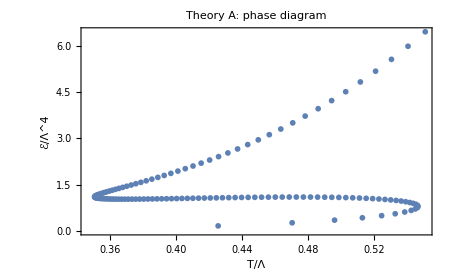

```mathematica
plotphaseA = ListPlot[
  Transpose[{thermo[[All, 1]]/thermo[[All, 3]],
    thermo[[All, 5]]/thermo[[All, 3]]^4}],
  Frame -> True, FrameLabel -> {"T/Λ", "ℰ/Λ^4"},
  PlotLabel -> "Theory A: phase diagram",
  PlotRange -> All, ImageSize -> 450]
```

### QNMs: q^2 for phiM = 0.8

prec sets the working precision in decimal digits. NQNMs sets the number of retained modes; GetQNM computes the full spectrum.

```mathematica
prec = 30;
Nu = Dimensions[fields][[3]];
grid = Cheb[0, 1, Nu, prec];
u = grid[[1]];

eigenfunctions = False;
NQNMs = 10;
tol = 10^-8;
```

For each background in the loop range, select the ten nonzero eigenvalues of smallest absolute value.

```mathematica
manymodes = {};

Monitor[
  Do[
    number = n;
    T = thermo[[number, 1]];
    QNM1 = GetQNM[grid, fields[[number]], VV, T, prec, NQNMs, eigenfunctions];

    QNM1 = Select[QNM1, NumberQ[#] && Abs[#] > tol &];
    qsquared = If[QNM1 === {}, {},
      MinimalBy[QNM1, Abs, Min[NQNMs, Length[QNM1]]]];
    If[Length[qsquared] < NQNMs,
      Print["Background ", number, ": only ", Length[qsquared], " modes selected."]];
    AppendTo[manymodes, {thermo[[number, 7]], qsquared}];
    , {n, 1, Nbackgrounds}],
  number
];
```

Extract the lightest mode from the same calculation.

```mathematica
dataqsquared = Table[
  {manymodes[[n, 1]],
   If[manymodes[[n, 2]] === {}, Missing["NoMode"], First[manymodes[[n, 2]]]]},
  {n, 1, Length[manymodes]}];
```

Plot the real parts of the ten selected eigenvalues. The saved data retain their imaginary parts.

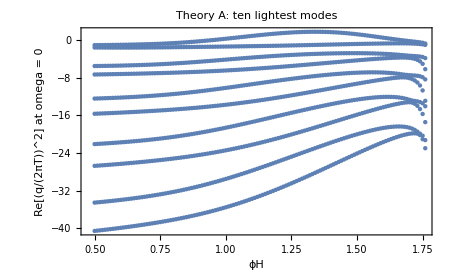

```mathematica
manymodespoints = Flatten[
  Table[
    Transpose[{ConstantArray[manymodes[[n, 1]], Length[manymodes[[n, 2]]]],
      Re[manymodes[[n, 2]]]}],
    {n, 1, Length[manymodes]}], 1];

plotmanyA = ListPlot[manymodespoints,
  Frame -> True,
  FrameLabel -> {"ϕH", "(q/(2πT))^2 at omega = 0"},
  PlotLabel -> "Theory A: ten lightest modes",
  PlotStyle -> PointSize[0.007], PlotRange -> All, ImageSize -> 450]
```

Plot the lightest nonzero mode.

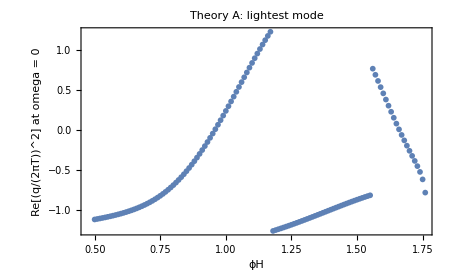

```mathematica
plotlightestA = ListPlot[
  {#[[1]], Re[#[[2]]]} & /@ Select[dataqsquared, NumberQ[#[[2]]] &],
  Frame -> True,
  FrameLabel -> {"ϕH", "Re[(q/(2πT))^2] at omega = 0"},
  PlotLabel -> "Theory A: lightest mode",
  PlotRange -> All, ImageSize -> 450]
```

Select the mode with the largest real part among the retained eigenvalues and plot its real part. This follows the upper envelope if branches cross.

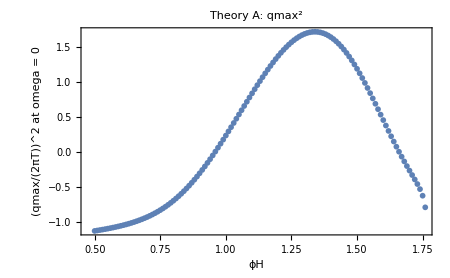

```mathematica
dataupperA = Table[
  {manymodes[[n, 1]],
   If[manymodes[[n, 2]] === {}, Missing["NoMode"],
    First[MaximalBy[manymodes[[n, 2]], Re]]]},
  {n, 1, Length[manymodes]}];

plotupperA = ListPlot[
  {#[[1]], Re[#[[2]]]} & /@ Select[dataupperA, NumberQ[#[[2]]] &],
  Frame -> True,
  FrameLabel -> {"ϕH", "(qmax/(2πT))^2 at omega = 0"},
  PlotLabel -> Row[{"Theory A: ", Superscript["qmax", 2]}],
  PlotRange -> All, ImageSize -> 450]
```

### Save results

Save the spectra, upper-mode data and plots for this theory. Rerunning these cells overwrites the corresponding files.

```mathematica
manymodesA = manymodes;
dataqsquaredA = dataqsquared;

Put[manymodesA, "./Results/dataqsquaredmanymodes_phiM_0.8_N60.m"];
Put[dataqsquaredA, "./Results/dataqsquared_phiM_0.8_N60.m"];
Put[dataupperA, "./Results/qmax2_phiM_0.8_N60.m"];
Export["./Results/phasediagram_phiM_0.8.pdf", plotphaseA];
Export["./Results/manymodeszerofreq_phiM_0.8.pdf", plotmanyA];
Export["./Results/qmax2_phiM_0.8.pdf", plotupperA];
```

## Theory B: phiM = 1

### Load background

```mathematica
constants = {κ -> 1, ϕM -> 10/10, ϕQ -> 10, 𝒶 -> 0};

If[!FileExistsQ["Background_N60_phiM_1.m"],
  Print["Missing file: Background_N60_phiM_1.m"]; Abort[]];
{thermo, fields} = Get["Background_N60_phiM_1.m"];
ψHlist = thermo[[All, 7]];
Nbackgrounds = Length[ψHlist];
Print["Number of backgrounds: ", Nbackgrounds];
```

Number of backgrounds: 145

### Phase diagram

Plot the rescaled energy density as a function of the rescaled temperature.

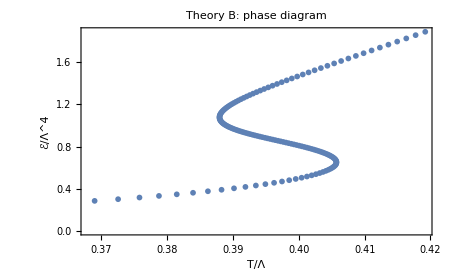

```mathematica
plotphaseB = ListPlot[
  Transpose[{thermo[[All, 1]]/thermo[[All, 3]],
    thermo[[All, 5]]/thermo[[All, 3]]^4}],
  Frame -> True, FrameLabel -> {"T/Λ", "ℰ/Λ^4"},
  PlotLabel -> "Theory B: phase diagram",
  PlotRange -> All, ImageSize -> 450]
```

### QNMs: q^2 for phiM = 1

prec sets the working precision in decimal digits. NQNMs sets the number of retained modes; GetQNM computes the full spectrum.

```mathematica
prec = 30;
Nu = Dimensions[fields][[3]];
grid = Cheb[0, 1, Nu, prec];
u = grid[[1]];

eigenfunctions = False;
NQNMs = 10;
tol = 10^-7;
```

For each background in the loop range, select the ten nonzero eigenvalues of smallest absolute value.

```mathematica
manymodes = {};

Monitor[
  Do[
    number = n;
    T = thermo[[number, 1]];
    QNM1 = GetQNM[grid, fields[[number]], VV, T, prec, NQNMs, eigenfunctions];

    QNM1 = Select[QNM1, NumberQ[#] && Abs[#] > tol &];
    qsquared = If[QNM1 === {}, {},
      MinimalBy[QNM1, Abs, Min[NQNMs, Length[QNM1]]]];
    If[Length[qsquared] < NQNMs,
      Print["Background ", number, ": only ", Length[qsquared], " modes selected."]];
    AppendTo[manymodes, {thermo[[number, 7]], qsquared}];
    , {n, 1, Nbackgrounds}],
  number
];
```

Extract the lightest mode from the same calculation.

```mathematica
dataqsquared = Table[
  {manymodes[[n, 1]],
   If[manymodes[[n, 2]] === {}, Missing["NoMode"], First[manymodes[[n, 2]]]]},
  {n, 1, Length[manymodes]}];
```

Plot the real parts of the ten selected eigenvalues. The saved data retain their imaginary parts.

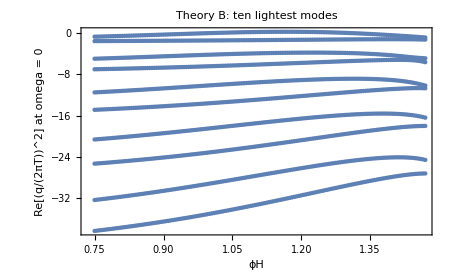

```mathematica
manymodespoints = Flatten[
  Table[
    Transpose[{ConstantArray[manymodes[[n, 1]], Length[manymodes[[n, 2]]]],
      Re[manymodes[[n, 2]]]}],
    {n, 1, Length[manymodes]}], 1];

plotmanyB = ListPlot[manymodespoints,
  Frame -> True,
  FrameLabel -> {"ϕH", "(q/(2πT))^2 at omega = 0"},
  PlotLabel -> "Theory B: ten lightest modes",
  PlotStyle -> PointSize[0.007], PlotRange -> All, ImageSize -> 450]
```

Plot the lightest nonzero mode.

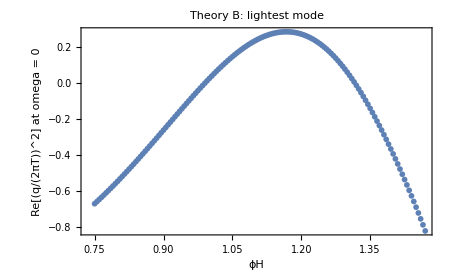

```mathematica
plotlightestB = ListPlot[
  {#[[1]], Re[#[[2]]]} & /@ Select[dataqsquared, NumberQ[#[[2]]] &],
  Frame -> True,
  FrameLabel -> {"ϕH", "(q/(2πT))^2 at omega = 0"},
  PlotLabel -> "Theory B: lightest mode",
  PlotRange -> All, ImageSize -> 450]
```

Select the mode with the largest real part among the retained eigenvalues and plot its real part. This follows the upper envelope if branches cross.

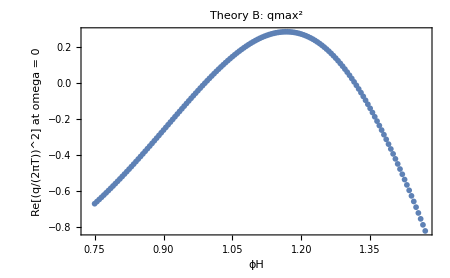

```mathematica
dataupperB = Table[
  {manymodes[[n, 1]],
   If[manymodes[[n, 2]] === {}, Missing["NoMode"],
    First[MaximalBy[manymodes[[n, 2]], Re]]]},
  {n, 1, Length[manymodes]}];

plotupperB = ListPlot[
  {#[[1]], Re[#[[2]]]} & /@ Select[dataupperB, NumberQ[#[[2]]] &],
  Frame -> True,
  FrameLabel -> {"ϕH", "(qmax/(2πT))^2 at omega = 0"},
  PlotLabel -> Row[{"Theory B: ", Superscript["qmax", 2]}],
  PlotRange -> All, ImageSize -> 450]
```

### Save results

Save the spectra, upper-mode data and plots for this theory. Rerunning these cells overwrites the corresponding files.

```mathematica
manymodesB = manymodes;
dataqsquaredB = dataqsquared;

Put[manymodesB, "./Results/dataqsquaredmanymodes_phiM_1_N60.m"];
Put[dataqsquaredB, "./Results/dataqsquared_phiM_1_N60.m"];
Put[dataupperB, "./Results/qmax2_phiM_1_N60.m"];
Export["./Results/phasediagram_phiM_1.pdf", plotphaseB];
Export["./Results/manymodeszerofreq_phiM_1.pdf", plotmanyB];
Export["./Results/qmax2_phiM_1.pdf", plotupperB];
```